(* Checking Alard 08 Fig 5 
MSSG; Sept 28, 2010
Output suppressed until plot by terminal semicolons *)

```mathematica
(* First deriv: df0/dtheta, see eq. 17 *)
```

```mathematica
dfdt[eta_,mp_, rp_,thetap_,theta_]=eta  Sin[2*theta] + mp rp Sin[theta-thetap] / Sqrt[1-2 rp Cos[theta-thetap] + rp^2];

f1[eta_,mp_, rp_,thetap_,theta_]=eta  Sin[2*theta] + mp  ( 1 - rp  Cos[theta-thetap]) / Sqrt[1-2 rp Cos[theta-thetap] + rp^2];
```

```mathematica
(* Plot with perturber at r_p = 0.75 -- green *)
p1 = Plot[dfdt[0, 1 , 0.75, 0, t],{t,-Pi,Pi}, PlotStyle->Red];
(* Plot with perturber at r_p = 0.75 -- green *)
p2 = Plot[dfdt[0, 1 , 0.9, 0, t],{t,-Pi,Pi}, PlotStyle->Green];(* Plot with perturber at r_p = 0.75 -- green *)
p3 = Plot[dfdt[0, 1 , 1.1, 0, t],{t,-Pi,Pi}, PlotStyle->Blue];(* Plot with perturber at r_p = 0.75 -- green *)
p4 = Plot[dfdt[0, 1 , 1.25, 0, t],{t,-Pi,Pi}, PlotStyle->Black];
```

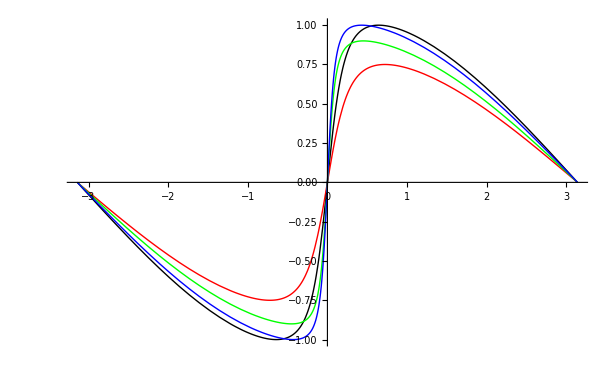

```mathematica
Show[p4,p1,p2,p3]
```

```mathematica
(* Show all together *)
```

```mathematica
(* Plot with perturber at r_p = 0.75 -- green *)
p1 = Plot[f1[0, 1 , 0.75, 0, t],{t,-Pi,Pi}, PlotStyle->Red];
(* Plot with perturber at r_p = 0.75 -- green *)
p2 = Plot[f1[0, 1 , 0.9, 0, t],{t,-Pi,Pi}, PlotStyle->Green];(* Plot with perturber at r_p = 0.75 -- green *)
p3 = Plot[f1[0, 1 , 1.1, 0, t],{t,-Pi,Pi}, PlotStyle->Blue];(* Plot with perturber at r_p = 0.75 -- green *)
p4 = Plot[f1[0, 1 , 1.25, 0, t],{t,-Pi,Pi}, PlotStyle->Black];
```

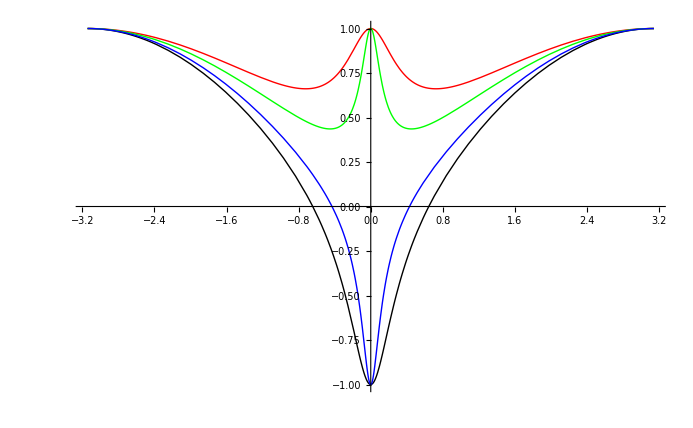

```mathematica
Show[p4,p1,p2,p3]
```